## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.15;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

25.2731

56.8725

56.8725

65.7086

65.257

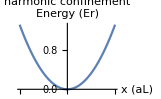

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-50,50},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

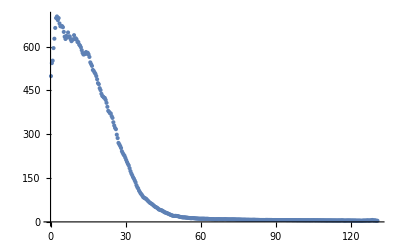

```mathematica
onsiteinteraction =0.407634 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174 ;
tunnelling= 0.12642;(*unit is Erecoil*)
tempβtest=1;(*1/(kB Temp) = 1/Er*)
nearestnum=6;

datainput=ToExpression[Import["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\data analysis\\2.5Er 3Aug 2017\\20G kick 0\\temp\\U_TempFitting_2.5Er_0Er_pulse_20G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin\\temp.txt","TSV"]];

datainput=Table[{datainput⟦ii,1⟧(0.18μm)/(λlat/2),datainput⟦ii,2⟧},{ii,1,Length[datainput]}];
ListPlot[datainput]
```

## Fitting fugacity, calculating double occupancy

```mathematica
partitionfunc[tempβ_,fugacity_,onsiteU_]:=1+2 (fugacity ) +fugacity^2 Exp[-tempβ onsiteU];
X2[tempβ_,fugacity_,onsiteU_]:=1/6 fugacity(1+fugacity^2 Exp[-tempβ onsiteU])+8 fugacity^2/(tempβ onsiteU)^2(1+Exp[-tempβ onsiteU])-16 fugacity^2/(tempβ onsiteU)^3(1-Exp[-tempβ onsiteU]);
X3[tempβ_,fugacity_,onsiteU_]:=1/3 fugacity(1+fugacity^2 Exp[-tempβ onsiteU])(1+2fugacity+fugacity^2 Exp[-tempβ onsiteU])+6 fugacity^2/(tempβ onsiteU) (1-2fugacity Exp[-tempβ onsiteU]+fugacity^2 Exp[-tempβ onsiteU] )-4 fugacity^2/(tempβ onsiteU)^2(2-Exp[-tempβ onsiteU]-2fugacity(1-2Exp[-tempβ onsiteU])+fugacity^2 Exp[-tempβ onsiteU](2-Exp[-tempβ onsiteU]))+4 fugacity^2/(tempβ onsiteU)^3(1-Exp[-tempβ onsiteU])(1+2fugacity +fugacity^2 Exp[-tempβ onsiteU]);
X4[tempβ_,fugacity_,onsiteU_]:=4 fugacity^2(1+fugacity^2 Exp[-tempβ onsiteU])^2+16 fugacity^3/(tempβ onsiteU) (1-Exp[-tempβ onsiteU])(1+fugacity^2 Exp[-tempβ onsiteU])+16 fugacity^4/(tempβ onsiteU)^2(1-Exp[-tempβ onsiteU])^2;
X5[tempβ_,fugacity_,onsiteU_]:=2/3 fugacity(1-4fugacity+fugacity^2+fugacity^4 Exp[-tempβ onsiteU] -4 fugacity^5 Exp[-tempβ onsiteU]^2+fugacity^6 Exp[-tempβ onsiteU]^3)+8 fugacity^2/(tempβ onsiteU)^1(1-fugacity+fugacity(1-2fugacity-fugacity^3)Exp[-tempβ onsiteU]+2 fugacity^3(1+fugacity)Exp[-tempβ onsiteU]^2)- 8 fugacity^2/(tempβ onsiteU)^2(2-fugacity-fugacity(1+8fugacity-fugacity^2)Exp[-tempβ onsiteU]+fugacity^3(1-2fugacity)Exp[-tempβ onsiteU]^2)+16 fugacity^2/(tempβ onsiteU)^3(1-fugacity-fugacity^2-(1-fugacity+2 fugacity^2+fugacity^3)Exp[-tempβ onsiteU]+fugacity^2(3+fugacity+fugacity^2)Exp[-tempβ onsiteU]^2-fugacity^4 Exp[-tempβ onsiteU]^3);
grandpotential[tempβ_,fugacity_,onsiteU_,tunnellingJ_]:=-1/tempβ Log[partitionfunc[tempβ,fugacity,onsiteU]]-1/tempβ((tempβ tunnellingJ)/partitionfunc[tempβ,fugacity,onsiteU])^2 nearestnum(fugacity+fugacity^3 Exp[-tempβ onsiteU]+2 fugacity^2(1-Exp[-tempβ onsiteU])/(tempβ onsiteU))-0 1/tempβ((tempβ tunnellingJ)/partitionfunc[tempβ,fugacity,onsiteU])^4(3*partitionfunc[tempβ,fugacity,onsiteU]^2*X2[tempβ,fugacity,onsiteU]+15*partitionfunc[tempβ,fugacity,onsiteU]*X3[tempβ,fugacity,onsiteU]-33/2*X4[tempβ,fugacity,onsiteU]+3*X5[tempβ,fugacity,onsiteU])
```

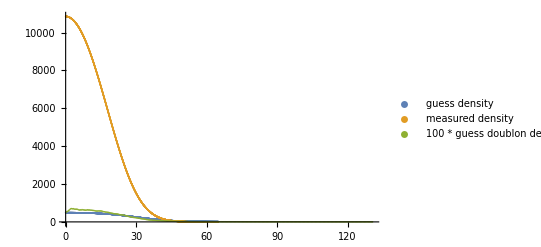

{14766.1,{fugacityfit→0.310929,tempβfit→4.07485,ampfit→1483.14,offsetfit→8.04639}}

```mathematica
leng=Length[datainput];
startind=5;endind=leng-50;
densityfunc[tempβ_,fugacity_,onsiteU_,tunnellingJ_,amp_,offset_]:=offset+amp*(-D[grandpotential[tempβ,fugacityx,onsiteU,tunnellingJ],fugacityx]/.fugacityx-> fugacity)tempβ fugacity;
doublonfunc[tempβ_,fugacity_,onsiteU_,tunnellingJ_,amp_,offset_]:=
amp*(D[grandpotential[tempβ,fugacity,onsiteUx,tunnellingJ],onsiteUx]/.onsiteUx-> onsiteU);
finaldensityfunc[tempβ_,fugacity_,onsiteU_,tunnellingJ_,amp_,offset_]:=densityfunc[tempβ,fugacity,onsiteU,tunnellingJ,amp,offset]-2*doublonfunc[tempβ,fugacity,onsiteU,tunnellingJ,amp,offset];

entropyfunc[tempβ_,fugacity_,onsiteU_,tunnellingJ_]:=(-D[grandpotential[tempβ,fugacityx,onsiteU,tunnellingJ],fugacityx]/.fugacityx-> fugacity)fugacity Log[fugacity]/tempβ (-tempβ^2)+
(-D[grandpotential[tempβx,fugacity,onsiteU,tunnellingJ],tempβx]/.tempβx-> tempβ)(-tempβ^2)

tempβguess=3;
fugacityguess=0.5;
ampguess=1000;
trapfguess=f0;
offsetguess=10;
finaldensityguess=Table[{ix,finaldensityfunc[tempβguess,fugacityguess*Exp[-tempβguess potential[ix,trapfguess]],onsiteinteraction,tunnelling,ampguess,offsetguess]},{ix,0,65,0.02}];
doublonguess=Table[{ix,100*doublonfunc[tempβguess,fugacityguess*Exp[-tempβguess potential[ix,trapfguess]],onsiteinteraction,tunnelling,ampguess,offsetguess]},{ix,0,65,0.02}];
ListPlot[{finaldensityguess,doublonguess,datainput},PlotLegends->{"guess density","measured density","100 * guess doublon density"},PlotRange->All]

χsquare=Total[Table[
(finaldensityfunc[tempβfit,fugacityfit*Exp[-tempβfit potential[datainput⟦ii,1⟧,f0]],onsiteinteraction,tunnelling,ampfit,offsetfit]-datainput⟦ii,2⟧)^2,
{ii,startind,endind}]];

sol=FindMinimum[{χsquare},{{fugacityfit,fugacityguess},{tempβfit,tempβguess},{ampfit,ampguess},{offsetfit,offsetguess}}]
(*sol=FindMinimum[{χsquare,μfit>-100,0.01<tempβfit<100,0<ampfit,10<trapffit<80},{{μfit,μguess},{tempβfit,tempβguess},{ampfit,ampguess},{trapffit,trapfguess}}]*)

(*
nlm=NonlinearModelFit[datainput,{densityfunc[tempβfit,μfit-potential[x,trapffit],onsiteinteraction,tunnelling,ampfit],μfit>-100,0.01<tempβfit<100,0<ampfit,10<trapffit<100},{{μfit,μguess},{tempβfit,tempβguess},{ampfit,ampguess},{trapffit,trapfguess}},x]
*)
```

```mathematica
sol⟦2,2,2⟧
sol⟦2,1,2⟧
sol⟦2,3,2⟧
sol⟦2,4,2⟧
```

4.07485

0.310929

1483.14

8.04639

fugacity is: 0.310929

temperature is 52.9714 (nK)

U/6J is 0.124409

β6J is 3.09086

chemical potential: -61.8808  nK

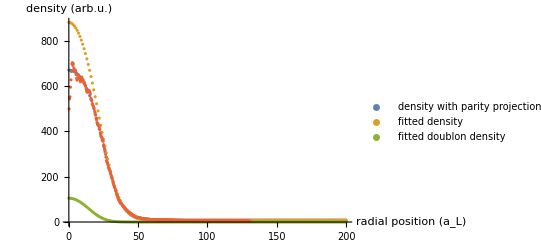

```mathematica
temβfitx=sol⟦2,2,2⟧;
fugacityfitx=sol⟦2,1,2⟧;
ampfitx=sol⟦2,3,2⟧;
offsetfitx=sol⟦2,4,2⟧;

(*temperature*)
tempnK=1/temβfitx Erecoil/(kB nK);
Print[StringJoin["fugacity is: ", ToString[fugacityfitx]]];
Print[StringJoin["temperature is ",ToString[tempnK]," (nK)"]]
Print[StringJoin["U/6J is ", ToString[onsiteinteraction/(6  tunnelling)]]];
Print[StringJoin["β6J is ",ToString[(6  tunnelling Erecoil)/(kB tempnK nK)]]];
(*chemical potential*)
chemicalpnK=Quiet[NSolve[Exp[chemicalpnKx/tempnK]==fugacityfitx,chemicalpnKx]]⟦1,1,2⟧;
Print[StringJoin["chemical potential: ",ToString[chemicalpnK],"  nK"]];
densityfit=Table[{ix,densityfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[ix,f0]],onsiteinteraction,tunnelling,ampfitx,offsetfitx]},{ix,0,200,1}];
doublonfit=Table[{ix,doublonfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[ix,f0]],onsiteinteraction,tunnelling,ampfitx,offsetfitx]},{ix,0,200,1}];
finaldensityfit=Table[{ix,finaldensityfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[ix,f0]],onsiteinteraction,tunnelling,ampfitx,offsetfitx]},{ix,0,200,1}];
Show[ListPlot[{finaldensityfit,densityfit,doublonfit,datainput},PlotRange->All,PlotLegends->{"density with parity projection","fitted density","fitted doublon density"},AxesLabel->{"radial position (a_L)","density (arb.u.)"}, AxesStyle->Large]]
```

## Entropy Calculation

entropy per site (center of trap):

0.963163

filling (center of trap):

0.588521

entropy per atom (center of trap):

1.63658

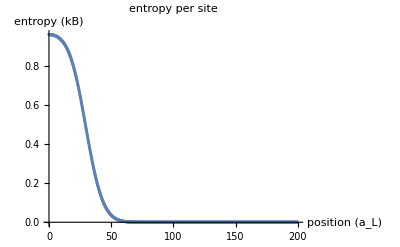
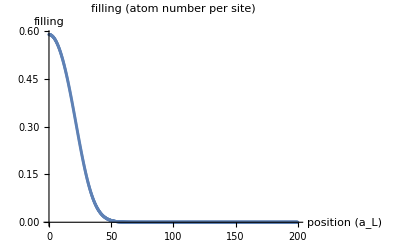
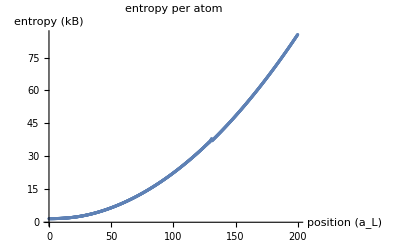

```mathematica
entropyfit=Table[{ix,entropyfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[ix,f0]],onsiteinteraction,tunnelling]},{ix,0,200,0.2}];
densityfit=Table[{ix,densityfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[ix,f0]],onsiteinteraction,tunnelling,1,0]},{ix,0,200,0.2}];
entropyls2=Table[{entropyfit⟦ii,1⟧,entropyfit⟦ii,2⟧/densityfit⟦ii,2⟧},{ii,1,Length[entropyfit]}];

Print["entropy per site (center of trap):"]
entropy00=entropyfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[00,f0]],onsiteinteraction,tunnelling]
Print["filling (center of trap):"]
den00=densityfunc[temβfitx,fugacityfitx*Exp[-temβfitx potential[00,f0]],onsiteinteraction,tunnelling,1,0]
Print["entropy per atom (center of trap):"]
entropy00/den00

{ListPlot[entropyfit,PlotRange->All,PlotLabel->"entropy per site",AxesLabel->{"position (a_L)"," entropy (kB)"}],ListPlot[densityfit,PlotRange->All,PlotLabel->"filling (atom number per site)",AxesLabel->{"position (a_L)"," filling"}],
ListPlot[entropyls2,PlotRange->All,PlotLabel->"entropy per atom",AxesLabel->{"position (a_L)"," entropy (kB)"}]}
```

### Average enetropy

```mathematica
f0horizontal=f0
f0vertical=√(fz^2+(xdtfreq*200/30)^2)
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;

dx=3;
dy=dx;
dz=dx/2;
densityf2[ix_,iy_,iz_]:=densityfunc[temβfitx,fugacityfitx*Exp[-temβfitx vext[ix,iy,iz]],onsiteinteraction,tunnelling,1,0];
entropyf2[ix_,iy_,iz_]:=entropyfunc[temβfitx,fugacityfitx*Exp[-temβfitx vext[ix,iy,iz]],onsiteinteraction,tunnelling];
doublonf2[ix_,iy_,iz_]:=doublonfunc[temβfitx,fugacityfitx*Exp[-temβfitx vext[ix,iy,iz]],onsiteinteraction,tunnelling,1,0];
Print["entropy3dls"]
entropy3dls=Flatten[Table[{entropyf2[iix,iiy,iiz]},{iix,-87,87,dx},{iiy,-87,87,dy},{iiz,-30,30,dz}]];
Print["density3dls"]
density3dls=Flatten[Table[{densityf2[iix,iiy,iiz]},{iix,-87,87,dx},{iiy,-87,87,dy},{iiz,-30,30,dz}]];
Print["doublon3dls"]
doublon3dls=Flatten[Table[{doublonf2[iix,iiy,iiz]},{iix,-87,87,dx},{iiy,-87,87,dy},{iiz,-30,30,dz}]];

naverage3dls=Table[(density3dls⟦ii⟧/2)^2,{ii,1,Length[density3dls]}];

Print["total number"]
totalnum=Total[density3dls]*dx dy dz
Print["average entropy per atom"]




totalentropy/totalnum

Vt=1/2 massK40 (2π (f0horizontal^2 f0vertical )^(1/3) )^2 (λlat/2 )^2;
Print["ρ"];
rho1=(Vt/(6  tunnelling Erecoil)  )^(3/2)totalnum
Print["doublon fraction:"]
doublonfrac=(Total[doublon3dls]*dx dy dz)/totalnum
Print["averaged density:"]
navg=Total[naverage3dls]/Total[density3dls]
```

65.257

223.223

entropy3dls

density3dls

doublon3dls

total number

14609.3

average entropy per atom

4.21913

ρ

0.896645

doublon fraction:

0.0438392

averaged density:

0.0610134

Compressbility

df1[position_]:=-(D[gpf[tempnK nK,chemicalyyX,onsiteUyx,tunnellingyyx],chemicalyyX]/.chemicalyyX→( chemicalyyx-potential[position,f0]*Erecoil))
κf1[position_]:=D[-(D[gpf[tempnK nK,chemicalyyX,onsiteUyx,tunnellingyyx],chemicalyyX]/.chemicalyyX→chemicalyx),chemicalyx]/.chemicalyx→ ( chemicalyyx-potential[position,f0]*Erecoil)
κls1=Table[{ii,κf1[ii]},{ii,1,60,0.1}];
dls1=Table[{ii,df1[ii]},{ii,1,60,0.1}];
ls1=Table[{dls1⟦ii,1⟧,κls1⟦ii,2⟧/dls1⟦ii,2⟧/(1/(kB tempnK nK))},{ii,1,Length[dls1]}];
ListPlot[ls1,PlotRange→All,PlotLabel→"compressibility",AxesLabel→{"position(a_L)","κ/densitykB Temp"}]